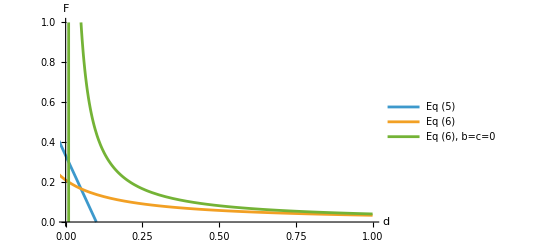

```mathematica
(*This script generates Fig. 3b in the main text, using stability criteria derived in the Supplementary Information Equations 5 and 6. Elsewhere we verified that these analytically derived stability criteria accurately capture the equilibria of our full population genetic model. Our full population genetic model can be run using our 'Run_Model.m' Matlab script. *)

(*Parameter values*)
b=0.3;
c=0.1;
s=0.05;
α=0.2;

(*Equation 5 in the SI solved for F. This shows when candidate greenbeards are stable against falsebeards*)
F5[d_]:=(c-d)/b;

(*Equation 6 in the SI solved for F. This shows when candidate greenbeards are stable against nonbeards*)
F6[d_]:=s (1-α)/(d-c+b-s α);

(*The below gives b=c=0 versions, i.e. stability conditions in the 'no altruism' scenario.*)
F5no[d_]:=0;  (*since d>0 gives vertical line at d=0*)
F6no[d_]:=s (1-α)/(d-s α);

Plot[{F5[d],F6[d],F6no[d]},{d,-0.1,1},PlotRange->{{0,1},{0,1}},AxesLabel->{"d","F"},PlotLegends->{"Eq (5)","Eq (6)","Eq (6), b=c=0"},Exclusions->None]

(*Add vertical line for Eq(5) when b=c=0*)
Show[%,Graphics[{Dashed,Line[{{0,0},{0,1}}]}]]

(*The graph below is reproduced (with some additional manual formatting not shown here) as Figure 3b in the main text. For the parameter values specified at the top of the script, candidate greenbeards are stable above the green line. They remain stable in the 'no altruism' scenario above the orange line. *)
```